## (a)纯阻性串行电弧故障

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

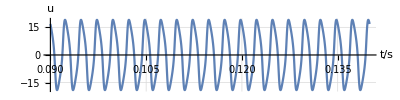

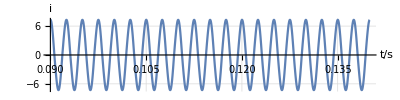

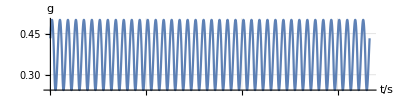

E_arc=

0.537175

融化体积V=

0.200007

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R i[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```

## (b)组感性串行电弧

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

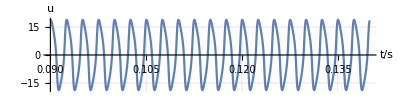

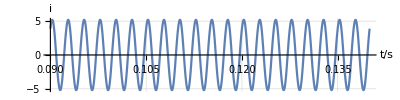

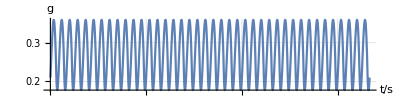

E_arc=

0.371337

融化体积V=

0.13826

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
L=R/(2π f);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R i[t]-L i'[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```

## (c)阻容性串行电弧

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

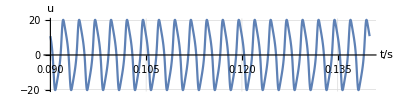

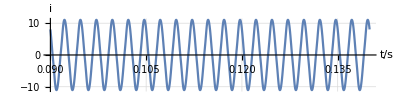

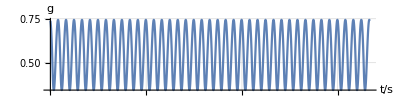

E_arc=

1.05698

融化体积V=

0.393546

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
c=1/(2π f R);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-uc[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[t]==uc[t]/R+c uc'[t],i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,uc},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```

## (d)纯阻性并行电弧

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

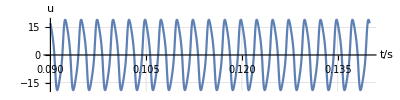

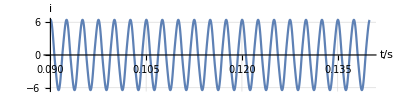

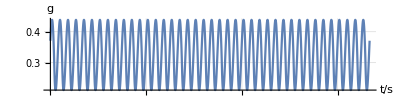

E_arc=

0.469285

融化体积V=

0.174729

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i[t]+u[t]/R),g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```

## (e)组感性并行电弧

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

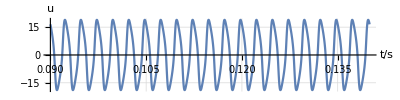

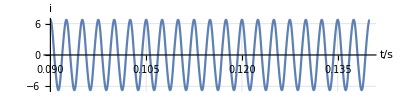

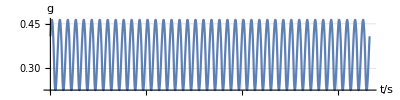

E_arc=

0.62023

融化体积V=

0.230931

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
L=R/(2π f);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i2[t]+i[t]),u[t]==R i2[t]+L i2'[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,i2},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```

## (f)阻容性并行电弧

-Graphics-

NDSolve::ivres: 对于微分代数系统，NDSolve 已经计算了给出零残差的初始值，但是某些分量与指定的不同. 如果它们需要被满足，建议您对所有应变量和它们的导数给出初始条件.

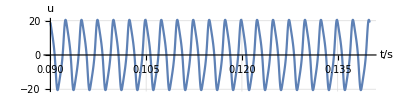

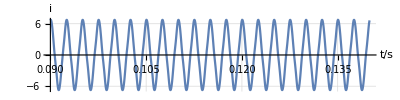

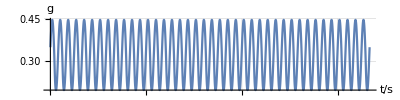

E_arc=

0.628088

融化体积V=

0.233857

```mathematica
Clear["Global`*"];
R=20;
t1=0.5 10^-3;

θ=t1/(√2);
p0=10;
U=17;
uarc=U/(√2);
ueff=115;
f=400;
c=1/(2π f R);
result=NDSolve[{u[t]==√2 ueff Cos[2π f t]-R (i2[t]+i[t]+c u'[t]),u[t]==R i2[t],g[t]u[t]==i[t],g'[t]==g[t]×1/θ((u[t]i[t])/Max[uarc×Abs[i[t]],p0]-1),i[0]==0,g[0]==100,u[0]==ueff},{u,i,g,i2},{t,0,0.2}];
result=result//Flatten;
u=u/.result⟦1⟧;
i=i/.result⟦2⟧;
g=g/.result⟦3⟧;
Plot[u[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电压",AxesLabel->{"t/s","u"}]
Plot[i[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电流",AxesLabel->{"t/s","i"}]
Plot[g[t],{t,0.09,0.14},AspectRatio->1/4,GridLines->Automatic,GridLinesStyle->Gray,PlotLegends->"电弧电导",AxesLabel->{"t/s","g"}]
"E_arc="
Earc=N[∫_0^0.01 u[t]i[t]ⅆt]
"融化体积V="
Earc/(660 904.144+3.98 10^5)×1/(2.7×10^3)10^9
```